#### Import MGenPackage

```mathematica
Block[{$Path=Append[$Path,NotebookDirectory[]]},
<<MGenPackage`]
```

#### Transform note string to a character

```mathematica
MGenPackage`Private`noteStrings
```

{A1,A#1,B1,C1,C#1,D1,D#1,E1,F1,F#1,G1,G#1,A2,A#2,B2,C2,C#2,D2,D#2,E2,F2,F#2,G2,G#2,A3,A#3,B3,C3,C#3,D3,D#3,E3,F3,F#3,G3,G#3,A4,A#4,B4,C4,C#4,D4,D#4,E4,F4,F#4,G4,G#4,A5,A#5,B5,C5,C#5,D5,D#5,E5,F5,F#5,G5,G#5,A6,A#6,B6,C6,C#6,D6,D#6,E6,F6,F#6,G6,G#6,A7,A#7,B7,C7,C#7,D7,D#7,E7,F7,F#7,G7,G#7, }

```mathematica
fromNoteString/@MGenPackage`Private`noteStrings
```

{-,.,/,0,1,2,3,4,5,6,7,8,9,:,;,<,=,>,?,@,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,[,\,],^,_,`,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,{,|,},~,.7f,.80, }

```mathematica
fromNoteCharacter/@fromNoteString/@MGenPackage`Private`noteStrings==MGenPackage`Private`noteStrings
```

True

#### All possible characters in string

```mathematica
MGenPackage`Private`characters
```

{@,^,_,-,+,=,~,`,{,[,},],|,\,<,>,.,;,?,/,:, ,.7f,.80,0,1,2,3,4,5,6,7,8,9,a,A,b,B,c,C,d,D,e,E,f,F,g,G,h,H,i,I,j,J,k,K,l,L,m,M,n,N,o,O,p,P,q,Q,r,R,s,S,t,T,u,U,v,V,w,W,x,X,y,Y,z,Z}

#### Import

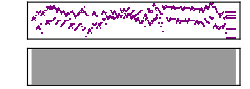

```mathematica
Import["/Users/peter.sjogren/Downloads/invent1.mid"]
```

```mathematica
data=Import["/Users/peter.sjogren/Downloads/invent1.mid"];
```

```mathematica
microsecondsPerQuarterNote=First@Cases[Import["/Users/peter.sjogren/Downloads/invent1.mid","Metadata"],("SetTempo"->tempo_)->tempo,{3}]
```

697674

#### Encode polyphonic MIDI as a string

A new 1/32 time slot will consist of either a blank “ “ which will mean that the time goes by or a character meaning a MIDI note followed by “+“ character to indicate the note length. On the same 1/32 time slot another note can start too.

```mathematica
a
```

-Graphics-

#### Convert to NoteChar, Begin32ndNote, Length32ndNote

```mathematica
noteStartlength=SortBy[data[[1]]/.SoundNote[note_,{fromTime_,toTime_},__,SoundVolume->__]->{fromNoteString@note,timeTo32ndNote@fromTime,timeTo32ndNote@(toTime-fromTime)},#[[2]]&];
%//Short[#,10]&
```

{{T,2,2},{V,4,2},{X,6,2},{Y,8,2},{V,10,2},{X,12,2},{T,14,2},{[,16,4},{H,18,2},{`,20,4},{J,20,2},{L,22,2},{M,24,2},{S,24,1},{Q,25,1},{J,26,2},{S,26,2},{`,28,4},{L,28,2},{H,30,2},{b,32,2},{O,32,4},{[,34,2},{C,36,4},{Q,36,2},{S,38,2},{`,40,2},{Q,42,2},«415»,{H,644,4},{Q,644,2},{[,646,2},{J,648,4},{Y,648,2},{Q,650,2},{[,652,2},{L,652,4},{R,654,2},{M,656,2},{Q,656,2},{J,658,2},{S,658,2},{`,660,2},{L,660,2},{M,662,2},{X,662,2},{O,664,4},{V,664,2},{`,666,2},{C,668,4},{Y,668,2},{S,670,2},{`,672,32},{[,672,32},{<,672,32},{H,672,32},{X,672,32}}

```mathematica
Differences[Join[{{" ",0,0}},noteStartlength][[All,2]]]
```

{2,2,2,2,2,2,2,2,2,2,0,2,2,0,1,1,0,2,0,2,2,0,2,2,0,2,2,2,2,2,2,2,2,0,2,2,0,1,1,0,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,2,2,2,2,0,2,2,0,1,1,0,2,2,0,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,1,1,2,0,2,0,1,1,2,0,2,2,2,2,2,2,2,2,2,2,2,2,0,2,2,0,2,2,0,2,2,0,2,2,2,2,2,2,2,2,2,2,0,2,2,0,2,2,0,2,2,0,2,2,2,2,2,2,2,2,2,2,0,2,2,0,2,2,0,2,2,0,2,2,2,2,2,2,2,2,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,2,2,2,2,0,2,2,0,1,1,0,2,2,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,2,0,2,2,0,1,1,2,0,2,2,0,2,2,0,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,2,0,1,1,0,2,0,2,0,2,0,2,2,0,2,2,0,2,2,0,2,2,0,2,0,2,0,2,0,2,0,2,2,0,2,2,0,0,0,0}

#### Convert to {note, numberOfClockAdvancesBeforeThisNote, noteLength}

```mathematica
clockAdvances=Differences[Join[{{" ",0,0}},noteStartlength][[All,2]]];
%//Short
```

{2,2,2,2,2,2,2,2,2,2,0,2,2,0,1,1,0,2,0,2,«431»,2,2,0,2,0,2,0,2,0,2,0,2,2,0,2,2,0,0,0,0}

Then convert each list to a string and StringJoin them.

```mathematica
noteAdvancesLengths=Transpose[{#[[1]],clockAdvances,#[[3]]}&@Transpose[noteStartlength]];
%//Short[#,10]&
```

{{T,2,2},{V,2,2},{X,2,2},{Y,2,2},{V,2,2},{X,2,2},{T,2,2},{[,2,4},{H,2,2},{`,2,4},{J,0,2},{L,2,2},{M,2,2},{S,0,1},{Q,1,1},{J,1,2},{S,0,2},{`,2,4},{L,0,2},{H,2,2},{b,2,2},{O,0,4},{[,2,2},{C,2,4},{Q,0,2},{S,2,2},{`,2,2},{Q,2,2},{S,2,2},{[,2,2},{b,2,4},{O,2,2},«407»,{J,0,2},{`,2,2},{L,0,4},{R,2,2},{H,2,4},{Q,0,2},{[,2,2},{J,2,4},{Y,0,2},{Q,2,2},{[,2,2},{L,0,4},{R,2,2},{M,2,2},{Q,0,2},{J,2,2},{S,0,2},{`,2,2},{L,0,2},{M,2,2},{X,0,2},{O,2,4},{V,0,2},{`,2,2},{C,2,4},{Y,0,2},{S,2,2},{`,2,32},{[,0,32},{<,0,32},{H,0,32},{X,0,32}}

```mathematica
StringJoin[{Array[" "&,#[[2]]],#[[1]],Array["+"&,#[[3]]-1]}&/@noteAdvancesLengths]
```

T+  V+  X+  Y+  V+  X+  T+  [+++  H+  `+++J+  L+  M+S Q J+S+  `+++L+  H+  b+O+++  [+  C+++Q+  S+  `+  Q+  S+  [+  b+++  O+  E+g+++  G+  eT+ d e+E+  g+++G+  O+  d+T+++  ]+  g+G+++  e+  d+T+++  g+  e+V+++  ]+  g+X+++  e+  d+O+++  b+  `+E+++  d+  b+G+++  e+  d+T+++  b+  `+L+++  S+  N+++Q+  `+  O+++S+  b+  `+E+++  S+  G+++Q+  [+  T+++++++++Z+  Q+  [+  S+  Q+++  J+  L+V+++  N+  `O+ S `+++L+  N+  b+J+  O+++S+  Q+  [+;+++  Z+  H+++X+  [+  J+++Z+  Q+  [+L+++  S+  N+++Q+  `+  O+++S+  b+  `+L+++  d+  ;+++++b+  S ` b+  g+H+  J+++S ` S+  >+++Q+  [+  [+++  C+  9+  ;+  H+  9+  ;+  C+  J+++  [+  O+++Q+  S+  `+N+++  Q+  O+++S+  [+  E+Z+++  J+  L+  N+  O+  L+  N+  J+  E+++  Q+  S+V+++  `+  b+T+++  S+  `+V+++  Q+  O+S+++  [+  Y+  X+  V+  Y+  X+  [+  Y+++  b+  `+X+++  S+  Q+Y+++  `+  S+V+++  b+  `+++X+  Q+  [+  Y+  X+  [+  Y+  Q+  [+++  d+  b+Y+++  `+  [+++S+  b+  a+X+++  d+  b+++Y+  R+  a+++Q+  [+  b+++Y+  Q+  [+d+++  R+  e+++Q+  [+  Q+++Y+  X+  S+++V+  Y+  a+++X+  [+  b+++Y+  X+  V+Z+++  T+  \+++G+  V+  Q+++T+  X+  S+++V+  T+  `+++G+  E+  b+++++++P+  G+  E+  T+  G+++  X+  L+++Z+  \+  Q+V T V+++Z+  \+  X+  d+T+  b+G+  `+E+  d+O+  b+N+  `+E+  P+S+  b+G+  `+E+  ]+T+  G+h+  _+V+  ]+T+  d+X+  e+V+  b+Y+  \+X+++  e+  d+E+++  b+  `X+++ b `+  L+++S+  Q+  E+++Q+  ]+  9+++g+  e+  d+  g+  e+  ]+  g+++++++++++++++++  X+  V+  T+  G+  V+  U+  X+  V+++++++++++++++++  d+  e+  g+  ]+  e+  g+  d+  e+++++++++++++++  E+  G+  T+  V+  G+  T+  E+  G+++++++++++++++++  g+  e+  d+  b+  e+  d+  g+  e+++++++++++++++++  V+  T+  G+  E+  T+  G+  V+  T+++++++++++++++++  b+  d+  e+  g+  d+  e+  b+  d+++++++++++++++++  O+  E+  F+  T+  E+  F+  O+  E+++  `+  b+F+++  d+  e+E+++  b+  d+O+++  `+  b+M+++  d+  e+V+++  g+  ]+T+++  e+  F+++g+  d+  e+E+++  g+  ]+Y+++  _+  l+X+++  ]+  _+V+++  g+  l+++X+  J+  g+++L+  M+  dO+ e d+L+  b+M+  `+J+  `+L+++  R+  H+++Q+  [+  J+++Y+  Q+  [+L+++  R+  M+Q+  J+S+  `+L+  M+X+  O+++V+  `+  C+++Y+  S+  `+++++++++++++++++++++++++++++++[+++++++++++++++++++++++++++++++<+++++++++++++++++++++++++++++++H+++++++++++++++++++++++++++++++X+++++++++++++++++++++++++++++++

#### Test notesToString

```mathematica
testString=polyphonicMIDIToString[FileNameJoin[{NotebookDirectory[],"Bach MIDI","invent","invent1.mid"}]];
testString//InputForm
```

"  T+  V+  X+  Y+  V+  X+  T+  [+++  H+  `+++J+  L+  M+S Q J+S+  `+++L+  H+  b+O+++  [+  C+++Q+  S+  `+  Q+  S+  [+  b+++  O+  E+g+++  G+  \
eT+ d e+E+  g+++G+  O+  d+T+++  ]+  g+G+++  e+  d+T+++  g+  e+V+++  ]+  g+X+++  e+  d+O+++  b+  `+E+++  d+  b+G+++  e+  d+T+++  b+  `+L+++  \
S+  N+++Q+  `+  O+++S+  b+  `+E+++  S+  G+++Q+  [+  T+++++++++Z+  Q+  [+  S+  Q+++  J+  L+V+++  N+  `O+ S `+++L+  N+  b+J+  O+++S+  Q+  \
[+;+++  Z+  H+++X+  [+  J+++Z+  Q+  [+L+++  S+  N+++Q+  `+  O+++S+  b+  `+L+++  d+  ;+++++b+  S ` b+  g+H+  J+++S ` S+  >+++Q+  [+  [+++  C+  \
9+  ;+  H+  9+  ;+  C+  J+++  [+  O+++Q+  S+  `+N+++  Q+  O+++S+  [+  E+Z+++  J+  L+  N+  O+  L+  N+  J+  E+++  Q+  S+V+++  `+  b+T+++  S+  \
`+V+++  Q+  O+S+++  [+  Y+  X+  V+  Y+  X+  [+  Y+++  b+  `+X+++  S+  Q+Y+++  `+  S+V+++  b+  `+++X+  Q+  [+  Y+  X+  [+  Y+  Q+  [+++  d+  \
b+Y+++  `+  [+++S+  b+  a+X+++  d+  b+++Y+  R+  a+++Q+  [+  b+++Y+  Q+  [+d+++  R+  e+++Q+  [+  Q+++Y+  X+  S+++V+  Y+  a+++X+  [+  b+++Y+  \
X+  V+Z+++  T+  \\+++G+  V+  Q+++T+  X+  S+++V+  T+  `+++G+  E+  b+++++++P+  G+  E+  T+  G+++  X+  L+++Z+  \\+  Q+V T V+++Z+  \\+  X+  d+T+  \
b+G+  `+E+  d+O+  b+N+  `+E+  P+S+  b+G+  `+E+  ]+T+  G+h+  _+V+  ]+T+  d+X+  e+V+  b+Y+  \\+X+++  e+  d+E+++  b+  `X+++ b `+  L+++S+  Q+  \
E+++Q+  ]+  9+++g+  e+  d+  g+  e+  ]+  g+++++++++++++++++  X+  V+  T+  G+  V+  U+  X+  V+++++++++++++++++  d+  e+  g+  ]+  e+  g+  d+  \
e+++++++++++++++  E+  G+  T+  V+  G+  T+  E+  G+++++++++++++++++  g+  e+  d+  b+  e+  d+  g+  e+++++++++++++++++  V+  T+  G+  E+  T+  G+  V+  \
T+++++++++++++++++  b+  d+  e+  g+  d+  e+  b+  d+++++++++++++++++  O+  E+  F+  T+  E+  F+  O+  E+++  `+  b+F+++  d+  e+E+++  b+  d+O+++  `+  \
b+M+++  d+  e+V+++  g+  ]+T+++  e+  F+++g+  d+  e+E+++  g+  ]+Y+++  _+  l+X+++  ]+  _+V+++  g+  l+++X+  J+  g+++L+  M+  dO+ e d+L+  b+M+  \
`+J+  `+L+++  R+  H+++Q+  [+  J+++Y+  Q+  [+L+++  R+  M+Q+  J+S+  `+L+  M+X+  O+++V+  `+  C+++Y+  S+  \
`+++++++++++++++++++++++++++++++[+++++++++++++++++++++++++++++++<+++++++++++++++++++++++++++++++H+++++++++++++++++++++++++++++++X++++++++++++\
+++++++++++++++++++"

```mathematica
Length[Cases[Characters[testString]," "]]/8/4
```

0

TODO: Add clock advance “ “ characters to the end so that all notes can have its full length.

#### Convert back to Sound object from string

No sequence of SoundNote. SoundNote objects that start at a time and ends at a time.

```mathematica
notesAndDurations=StringCases[testString,{b:(" "..):>{" ",StringLength[b]},note_~~p:("+"..):>{note,1+StringLength[p]}}];
notesAndDurations//Short[#,10]&
```

{{ ,2},{T,2},{ ,2},{V,2},{ ,2},{X,2},{ ,2},{Y,2},{ ,2},{V,2},{ ,2},{X,2},{ ,2},{T,2},{ ,2},{[,4},{ ,2},{H,2},{ ,2},{`,4},{J,2},{ ,2},{L,2},{ ,2},{M,2},{ ,1},{ ,1},{J,2},{S,2},{ ,2},{`,4},{L,2},{ ,2},{H,2},{ ,2},{b,2},{O,4},{ ,2},{[,2},{ ,2},«720»,{[,2},{ ,2},{J,4},{Y,2},{ ,2},{Q,2},{ ,2},{[,2},{L,4},{ ,2},{R,2},{ ,2},{M,2},{Q,2},{ ,2},{J,2},{S,2},{ ,2},{`,2},{L,2},{ ,2},{M,2},{X,2},{ ,2},{O,4},{V,2},{ ,2},{`,2},{ ,2},{C,4},{Y,2},{ ,2},{S,2},{ ,2},{`,32},{[,32},{<,32},{H,32},{X,32}}

```mathematica
notesStartsAndDurations=Cases[FoldList[If[#2[[1]]==" ",{#2[[1]],#1[[2]]+#2[[2]],#2[[2]]},{#2[[1]],#1[[2]],#2[[2]]}]&,{" ",0,0},notesAndDurations],
Except[{" ",_,_}]];
notesStartsAndDurations//Short[#,10]&
```

{{T,2,2},{V,4,2},{X,6,2},{Y,8,2},{V,10,2},{X,12,2},{T,14,2},{[,16,4},{H,18,2},{`,20,4},{J,20,2},{L,22,2},{M,24,2},{J,26,2},{S,26,2},{`,28,4},{L,28,2},{H,30,2},{b,32,2},{O,32,4},{[,34,2},{C,36,4},{Q,36,2},{S,38,2},{`,40,2},{Q,42,2},{S,44,2},{[,46,2},«399»,{H,644,4},{Q,644,2},{[,646,2},{J,648,4},{Y,648,2},{Q,650,2},{[,652,2},{L,652,4},{R,654,2},{M,656,2},{Q,656,2},{J,658,2},{S,658,2},{`,660,2},{L,660,2},{M,662,2},{X,662,2},{O,664,4},{V,664,2},{`,666,2},{C,668,4},{Y,668,2},{S,670,2},{`,672,32},{[,672,32},{<,672,32},{H,672,32},{X,672,32}}

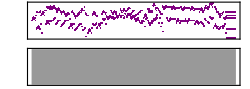

```mathematica
Sound[SoundNote[fromNoteCharacter[#[[1]]],{note32ndToTime[#[[2]],120],note32ndToTime[#[[2]],120]+note32ndToTime[#[[3]],120]}]&/@notesStartsAndDurations]
```

```mathematica
stringToSound[string_,tempoBPM_]:=Module[{notesAndDurations,notesStartsAndDurations},
notesAndDurations=StringCases[string,{b:(" "..):>{" ",StringLength[b]},note_~~p:("+"...):>{note,1+StringLength[p]}}];
notesStartsAndDurations=Cases[FoldList[If[#2[[1]]==" ",{#2[[1]],#1[[2]]+#2[[2]],#2[[2]]},{#2[[1]],#1[[2]],#2[[2]]}]&,{" ",0,0},notesAndDurations],
Except[{" ",_,_}]];
Sound[Cases[SoundNote[fromNoteCharacter[#[[1]]],{note32ndToTime[#[[2]],tempoBPM],note32ndToTime[#[[2]],tempoBPM]+note32ndToTime[#[[3]],tempoBPM]}]&/@notesStartsAndDurations,
Except[SoundNote[" ",{_,_}]]
]
]
]
```

#### Test conversion from MIDI to string and back

```mathematica
ImportString[ExportString[stringToSound[polyphonicMIDIToString[FileNameJoin[{NotebookDirectory[],"Bach MIDI","invent","invent1.mid"}]],80],"WAV"],"WAV"]
```

#### Train a recurrent neural network

All Bach inventions concatenated to one string

```mathematica
text=StringJoin[polyphonicMIDIToString/@FileNames[FileNameJoin[{NotebookDirectory[],"Bach MIDI","invent","invent*.mid"}]]];
text//StringLength
text//Short[#,10]&
```

38953

[+++    S+++    b+++    S+++    [+++    b+++    S+++    [+++    g+++    f+J+++  g+  f+++N+++    b+++E+++    ]+++N+++    f+++J+++    b+++E+++    ]+++N+++    f+++J+++    b+++T+++    g+++G+  T+  b+++G+++    O+++S+++    e+++V+++    b+++G+++    O+++S+++    e+++V+++    b+++G+++    O+++S+++    d+++T+++    `+++X+++    Q+++T+++    E+++Z+++    Q+++T+++    `+++E+++    d+++N+++    b+++O+++    `+++E+++    b+++G+++    S+++V+++    [+++G+++    O+++X+++    [+++G+++    O+++S+++    b+++L+++    `+++N+++    O+++S+++    `+++E+++    Q+++T+++ … R+  \+T+  [+F+  \+P+  O+R+++++++++  M+  L+  O+  H+++++++++  \+  [+  Y+  X+  J+Y+  [+L+  \+M+  O+R+  `+P+  a+F+  O+R+  `+P+  F+R+  \+T+++++  [+  \+++  F+  P+Y+++  O+  a+++++++++M+  K+  I+  H+  :+  `+H+  I+++++R+  Q+  R+++  H+  [+++:+  D+  C+d+++++++++  A+  @+  >+  <+  >+e+  @+g+  A+h+  ^+++C+  D+  :+g+  C+d+  a+++A+  @+  `+++A+  @+  A+++++++R+  \+  [+  \+  R+  a+H+  `+J+  L+R+  \+M+  [+L+  M+Y+  O+X+  `+++++P+  O+  P+  a+F+  [T+++ \ [ \ [F+++ \ [ \ [+++T+++    H+++Y+++    A+++++++++++++++++++++++Y+++++++++++++++++++++++

#### Load the document Flute to import necessary functions

```mathematica
trainingdata=sampleText[text,150,20000];
RandomSample[trainingdata,5]
generator=Function[sampleText[text,150,#BatchSize]];
```

{ ^+  l+  h+M+++++++  ^+  g+  h+  e+  h+  g+J+  h+H+  e+J+++  g+  c+K+++  e+  b+M K l+M+++++  _+  ]+  _+O+++++++  l+  ]+  _+  `+K+++  l+  ^+P+++  h+  ^+→O,+++    [+++F+  P+  c+++O+  P+  F+++R+++    [+++K+++    O+++R+  \+  [+:+++  \+  J+++R+++    H+++W+++++++    A+  C+  9+c+++++++++++  C+  A+++    H+++    →9, c+H+++  e+  c+H+  ;+b+  c+H+++  e+  b+J+++  c+  `+K J K+++++l+  ^+  l+  h+M+++++++  ^+  g+  h+  e+  h+  g+J+  h+H+  e+J+++  g+  c+K+++  e+  b+M K l+M+→+,  Q+++Z+  V+  f+++++G+  V+  O+  b+G+  S+V+  b+Z+  [+++X+  T+  d+++++E+  T+  N+  `+E+  Q+T+++++  `+  Z+  g+G+  f+T+  d+E+  c+G+++  f+  ;+++S+  c+  d+++L→+,+++  d+  e+++P+  F+  P+Y+  O+X+  P+Y+++  F+  [+++O+  P+  \M+ [ \+++++Y+  W+  Y+  R+++++++U+  W+  T+  U+  F+  U+  [+T+  U+Y+  [+++F+  T+  \+++P+  F+  O+→R}

#### Specify net

One LSTM layer

```mathematica
net4=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[100,"Dropout"->0.2],
SequenceLastLayer[],
LinearLayer[64],
Tanh,
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

More LSTM layers

```mathematica
net4=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[100,"Dropout"->0.0],
LongShortTermMemoryLayer[100,"Dropout"->0.0],
LongShortTermMemoryLayer[100,"Dropout"->0.0],
LongShortTermMemoryLayer[100,"Dropout"->0.0],
SequenceLastLayer[],
LinearLayer[64],
Tanh,
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

Deep

```mathematica
net4=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[30,"Dropout"->0.1],
LongShortTermMemoryLayer[30,"Dropout"->0.],
LongShortTermMemoryLayer[30,"Dropout"->0.],
LongShortTermMemoryLayer[30,"Dropout"->0.],
LongShortTermMemoryLayer[30,"Dropout"->0.],
SequenceLastLayer[],
LinearLayer[64],
Tanh,
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

Many

```mathematica
net4=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[500,"Dropout"->0.2],
SequenceLastLayer[],
LinearLayer[64],
Tanh,
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

```mathematica
trainedNet4=net4;
```

#### Train

With training set

```mathematica
trainedNet4=NetTrain[trainedNet4,trainingdata,BatchSize->512,TargetDevice->"CPU",MaxTrainingRounds->Quantity[8,"Hours"],TrainingProgressCheckpointing->{"Directory",FileNameJoin[{NotebookDirectory[],"PolyphonicCheckpoints1"}]}]
```

NetChain[]

```mathematica
copyFile[path_]:=Module[{list,file},
list=FileNameSplit[path];
file=list[[-1]];
CopyFile[path,FileNameJoin[{NotebookDirectory[],"PolyphonicNets",file}]
]]
```

```mathematica
copyFile["/Users/peter.sjogren/Google Drive/Mathematica/bach/PolyphonicCheckpoints1/2017-10-03T09:11:55_5_0294_05861_9.84e-1.wlnet"]
```

/Users/peter.sjogren/Google Drive/Mathematica/bach/PolyphonicNets/2017-10-03T09:11:55_5_0294_05861_9.84e-1.wlnet

#### Sample LSTM[100] net for a sequence

After 1 minute

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-02T09:24:14_4_0002_00021_3.03e+0.wlnet"}]];
```

After 10 minutes

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-02T09:33:03_5_0011_00201_1.53e+0.wlnet"}]];
```

After 1 hour

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-02T09:53:29_8_0276_05501_5.13e-1.wlnet"}]];
```

After 2 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-02T10:59:33_9_0645_12881_1.84e-1.wlnet"}]]
```

After 4 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-02T13:04:01_10_0878_17541_9.45e-2.wlnet"}]]
```

After 5 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-02T15:56:17_11_261_5201_8.98e-2.wlnet"}]]
```

NetChain[]

After 8 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-02T18:55:52_1_1306_26101_8.97e-2.wlnet"}]]
```

NetChain[]

After 15 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-02T22:54:26_2_2557_51121_4.66e-2.wlnet"}]]
```

```mathematica
characters
```

{@,^,_,-,+,=,~,`,{,[,},],|,\,<,>,.,;,?,/,:, ,.7f,.80,0,1,2,3,4,5,6,7,8,9,a,A,b,B,c,C,d,D,e,E,f,F,g,G,h,H,i,I,j,J,k,K,l,L,m,M,n,N,o,O,p,P,q,Q,r,R,s,S,t,T,u,U,v,V,w,W,x,X,y,Y,z,Z}

Start with actual sequence from the material

```mathematica
toWAVSound[stringToSound[generateSample[trainedNet4,"`+++E+++    b+++G+++    S+++V+++    [+++G+++",1000],80.]]
```

Start with blanks

```mathematica
toWAVSound[stringToSound[generateSample[trainedNet4,"    ",1000],80.]]
```

Start with random string

```mathematica
toWAVSound[stringToSound[StringDrop[generateSample[trainedNet4,StringJoin[RandomChoice[Flatten[Characters[characters]],30]],1000],30],60.]]
```

#### Sample {LSTM[30],LSTM[30],LSTM[30]} net for a sequence

After 1 hour

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-03T09:11:55_5_0294_05861_9.84e-1.wlnet"}]];
```

After 3 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-03T12:03:22_11_0643_12841_6.97e-1.wlnet"}]];
```

After 4 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-03T14:14:42_12_0321_06401_6.34e-1.wlnet"}]];
```

Start with actual sequence from the material

```mathematica
toWAVSound[stringToSound[generateSample[trainedNet4,"`+++E+++    b+++G+++    S+++V+++    [+++G+++",1000],80.]]
```

Start with blanks

```mathematica
toWAVSound[stringToSound[generateSample[trainedNet4,"    ",1000],80.]]
```

Start with random string

```mathematica
toWAVSound[stringToSound[StringDrop[generateSample[trainedNet4,StringJoin[RandomChoice[Flatten[Characters[characters]],30]],1000],30],80.]]
```

#### Sample {LSTM[100],LSTM[100],LSTM[100,LSTM[100]} net for a sequence

After 4 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-03T16:53:02_15_020_00381_1.28e+0.wlnet"}]];
```

After 8 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-03T16:53:02_15_522_10421_1.40e-3.wlnet"}]];
```

After 16 hours

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-03T21:33:19_16_0940_18786_1.35e-4.wlnet"}]];
```

Some low loss

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-03T21:33:19_16_0579_11561_2.03e-5.wlnet"}]];
```

Start with actual sequence from the material

```mathematica
toWAVSound[stringToSound[generateSample[trainedNet4,"`+++E+++    b+++G+++    S+++V+++    [+++G+++",1000],80.]]
```

Start with blanks

```mathematica
toWAVSound[stringToSound[generateSample[trainedNet4,"    ",1000],80.]]
```

Start with random string

```mathematica
toWAVSound[stringToSound[StringDrop[generateSample[trainedNet4,StringJoin[RandomChoice[Flatten[Characters[characters]],30]],1000],30],80.]]
```

#### Sample {LSTM[10],LSTM[10],LSTM[10],LSTM[10],LSTM[10],LSTM[10],LSTM[10],LSTM[10],LSTM[10],LSTM[10]} net for a sequence

After 10 hours. Learns slow!

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-04T22:46:07_23_1197_23940_1.09e+0.wlnet"}]];
```

Start with actual sequence from the material

```mathematica
toWAVSound[sound=stringToSound[generateSample[trainedNet4,"`+++E+++    b+++G+++    S+++V+++    [+++G+++",1000],80.]]
```

Start with blanks

```mathematica
toWAVSound[sound=stringToSound[generateSample[trainedNet4,"    ",1000],80.]]
```

Start with random string

```mathematica
toWAVSound[sound=stringToSound[StringDrop[generateSample[trainedNet4,StringJoin[RandomChoice[Flatten[Characters[characters]],30]],1000],30],80.]]
```

#### Sample from {LSTM[500]} net. examples with 150 characters as input sequence instead of 50.

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-06T10:19:04_1_006_0201_6.08e-1.wlnet"}]]
```

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-06T15:37:59_4_06_0201_2.89e-1.wlnet"}]]
```

This is pretty interesting. Go with this.

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-06T18:46:07_6_036_1401_1.18e-1.wlnet"}]]
```

NetChain[]

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-06T22:21:22_7_082_3245_3.07e-2.wlnet"}]]
```

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-07T10:16:50_0_063_2481_5.13e-2.wlnet"}]]
```

I think this is stuck in a local maximum - lots of sequences with repeating notes.

```mathematica
trainedNet4=Import[FileNameJoin[{NotebookDirectory[],"PolyphonicNets","2017-10-07T16:33:04_1_042_1641_2.53e-2.wlnet"}]]
```

NetChain[]

```mathematica
toWAVSound[sound=stringToSound[generateSampleTruncated[trainedNet4,"`+++E+++    b+++G+++    S+++V+++    [+++G+++",1000],80.]]
```

```mathematica
toWAVSound[sound=stringToSound[generateSampleTruncated[trainedNet4,"    ",1000],80.]]
```

```mathematica
toWAVSound[sound=stringToSound[StringDrop[generateSampleTruncated[trainedNet4,StringJoin[RandomChoice[Flatten[Characters[characters]],30]],5000],30],80.]]
```

#### Make a NetGraph with LSTM state port

```mathematica
trained4graph=NetGraph[{trainedNet4[[1]],trainedNet4[[2]],trainedNet4[[3]],trainedNet4[[4]],trainedNet4[[5]],trainedNet4[[6]],trainedNet4[[7]]},

{1->2->3->4->5->6->7,NetPort[2,"State"]->NetPort["LSTMState"],NetPort[2,"CellState"]->NetPort["LSTMCellState"]},"Input"->NetEncoder[{"Characters",characters}]]
```

NetGraph[]

#### Sample the net and plot the state vectors in the output sequence as rows in a matrix

```mathematica
generateSampleFromGraphTruncated[net_,start_,len_]:=
Nest[Module[{result,output,state,cellstate},
result=net[StringTake[#[[1]],-Min[150,StringLength[#[[1]]]]]];
output=result["Output"];
cellstate=result["LSTMCellState"];
state=result["LSTMState"];
{StringJoin[#[[1]],
RandomSample[output->characters,1]
],Join[#[[2]],{state}],Join[#[[3]],{cellstate}]}]&,{start,{},{}},len]
```

#### Sample net graph and plot state vectors and cell state vectors as matrices

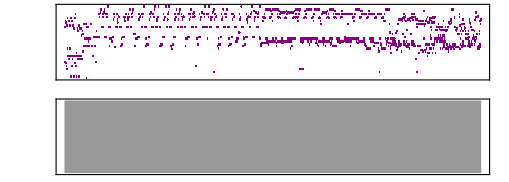

-Graphics-

-Graphics-

```mathematica
seed=StringJoin[RandomChoice[Flatten[Characters[characters]],30]];
{str,states,cellstates}=generateSampleFromGraphTruncated[trained4graph,seed,5000];
{#,toWAVSound[#]}&@stringToSound[StringDrop[str,StringLength[seed]],80.]
MatrixPlot[states]
MatrixPlot[cellstates]
```

#### TODO